-Graphics-                  -Graphics-

# 有限元(FEM)程序包在永磁电机电磁场分析中的应用

## 沈梦笑 mengxiaoshen@zju.edu.cn 导师：福义涛

## 目录

偏微分方程的数值计算

有限元计算原理

求解偏微分方程(NDSolveValue)

有限元程序包的使用

初始化 (Initialization Stage)

离散化 (Discretization Stage)

求解 (Solution Stage)

后处理 (Post-Processing)

数值计算与解析计算在永磁电机电磁场分析中的耦合与应用

课题组的工作

解析法原理与实现

耦合的实现

总结

## 1. 偏微分方程的数值计算

### 1.1 有限元计算原理

数学模型

(∂^2 A)/(∂x^2)+(∂^2 A)/(∂y^2)=-μJ
	s_1:A=A_0
	s_2:(∂A)/(∂n)=μq

变分法模型

W(A)=∫∫_Ω [1/μ((∂^2 A)/(∂x^2)+(∂^2 A)/(∂y^2))-JA]dxdy=min
	s_1:A=A_0
	s_2:(∂A)/(∂n)=μq

离散化模型

A^e=N_i A_i+N_j A_j+N_m A_m                   N:形状函数                     -Graphics-
	W_e(A)=∫∫_Ω_e [1/μ((∂^2 A^e)/(∂x^2)+(∂^2 A^e)/(∂y^2))-J_e A^e]dxdy=min      
	s_1:A^e=A_0^e
	s_2:(∂A^e)/(∂n)=μq^e

有限元矩阵

W(A)=1/2{A}^T[k]{A}-{A}{q}=min
	[K]{A}-{q}=0

[K]{A}={q}

### 1.2 求解偏微分方程(NDSolveValue)

偏微分方程 (A Partial Different Equation)

```mathematica
op=-Laplacian[u[x,y],{x,y}]-20
```

-20-u^(0,2)[x,y]-u^(2,0)[x,y]

求解域 (A Region)

```mathematica
Ω=ImplicitRegion[!((x-5)^2+(y-5)^2 ≤ 3^2),{{x,0,5},{y,0,10}}]
RegionPlot[Ω,AspectRatio->Automatic,ImageSize->150]
```

ImplicitRegion[(-5+x)^2+(-5+y)^2>9&&0≤x≤5&&0≤y≤10,{x,y}]

-Graphics-

边界条件 (Boundary Conditions)

{DirichletCondition[u[x,y]==0,x==0&&8≤y≤10],DirichletCondition[u[x,y]==100,(-5+x)^2+(-5+y)^2==9]}

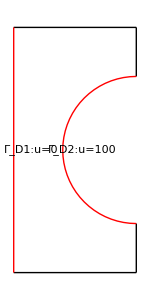

```mathematica
Subscript[Γ, D]={DirichletCondition[u[x,y]==0, x==0&&8≤y≤10],DirichletCondition[u[x,y]==100,(x-5)^2+(y-5)^2==3^2]}
picture=Graphics[{Line[{{5,0},{5,2}}],Line[{{5,10},{5,8}}],Line[{{0,10},{5,10}}],Line[{{0,0},{5,0}}],Opacity[1,Red],Thick,Line[{{0,0},{0,10}}],Circle[{5,5},3,{π/2,(3π)/2}],Black,Text["Γ_D1:u=0",{0.7,5}],Text["Γ_D2:u=100",{2.8,5}]},ImageSize->150]
```

求解方程 (Solve the PDE)

```mathematica
ufun=NDSolveValue[{op==0,Subscript[Γ, D]},u,{x,y}∈Ω]
```

InterpolatingFunction[…]

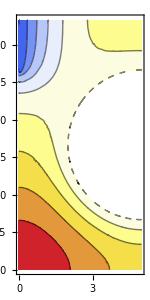

```mathematica
ContourPlot[ufun[x,y],{x,y}∈Ω,ColorFunction->"Temperature",AspectRatio->Automatic,ImageSize->150]
```

## 2. 有限元程序包的使用

```mathematica
Needs["NDSolve`FEM`"]
```

### 2.1 初始化 (Initialization Stage)

#### 2.1.1 变量数据和解数据 (Variable and Solution Data)

```mathematica
vd = NDSolve`VariableData[{"DependentVariables"->{u},"Space"->{x,y}}]
```

{None,{x,y},{u},{},{},{},{},{}}

```mathematica
(*parameter*)
```

```mathematica
n=93;Subscript[r, 1]=r1=0.083;Subscript[r, 2]=r2=0.0945;Subscript[r, 3]=r3=0.095;Subscript[r, 4] =r4= 0.145;Subscript[r, 5]=r5=0.160;
Subscript[rN, 1] =rN1=(r1+r2)/2;Subscript[rN, 2] =rN2=(r2+r3)/2;Subscript[rN, 3] =rN3= (r3+r4)/2;
μ1=1;p=2;q=1;bR=1.23;η=1;μAir=1;μB=5000*μAir;
```

```mathematica
jMax=6;δ=(2π)/jMax*0.7;α=0(*-π/20*);width=r3*Sin[(2 π/jMax-δ)/2];
cc=Table[If[i==1,0,If[i==2(jMax+1),2π,If[i/2∈Integers,Table[α+δ/2+(2π)/jMax*n,{n,0,jMax-1}]⟦i/2⟧,Table[α-δ/2+(2π)/jMax*n,{n,1,jMax}]⟦(i-1)/2⟧]]],{i,1,2(jMax+1)}];
ccc=Table[If[i==1,0,If[i==2(jMax+1),2π,If[i/2∈Integers,α+π/jMax+2 π/jMax(i/2-1)-ArcSin[width/r4],α+π/jMax+2 π/jMax((i-1)/2-1)+ArcSin[width/r4]]]],{i,1,2(jMax+1)}];
graphic=Graphics[{Table[Circle[{0,0},r3,{cc⟦i⟧,cc⟦i+1⟧}],{i,1,2jMax+1}],Circle[{0,0},r5],Line[Table[{{r3*Cos[cc⟦j⟧],r3*Sin[cc⟦j⟧]},{r4*Cos[ccc⟦j⟧],r4*Sin[ccc⟦j⟧]}},{j,2,2jMax+1}]],Table[Circle[{0,0},r4,{ccc⟦2 i+1⟧,ccc⟦2 i+2⟧}],{i,0,jMax}]}];
```

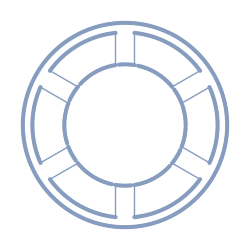

```mathematica
mr=DiscretizeGraphics[graphic,MaxCellMeasure->0.000004(*0.0002*),ImageSize->250]
```

```mathematica
bmesh=ToBoundaryMesh[mr,"MeshOrder"->1];
```

```mathematica
statorCoordinate1={(r4+r5)/2 Sin[-α],(r4+r5)/2 Cos[α]};
coilCoordinates=Table[{(r3+r4)/2 Cos[(2π)/jMax(n-1)],(r3+r4)/2 Sin[(2π)/jMax(n-1)]},{n,1,jMax}];
```

```mathematica
markerColors={Blue,Red};
markerCoordinates={(*{airCoordinate1},*){statorCoordinate1},{coilCoordinates}};
```

```mathematica
coilMarkers={2,3,4,5,6,7};
```

```mathematica
Short[markerSpecification=Join[{(*{airCoordinate1,1},*){statorCoordinate1,1}},MapThread[{#1,#2}&,{coilCoordinates,coilMarkers}]]];
```

```mathematica
mesh=ToElementMesh[bmesh,(*MaxCellMeasure->0.0001,"MaxBoundaryCellMeasure"->0.5,*)"RegionMarker"->markerSpecification,"RegionHoles"->{{0,0}},"MeshOrder"->1(*"NodeReordering"->True,*)]
```

ElementMesh[{{-0.159993,0.16},{-0.159998,0.159998}},{TriangleElement[<4183>]}]

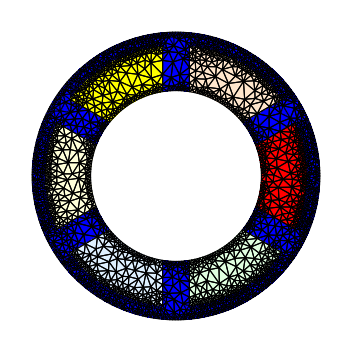

```mathematica
mesh["Wireframe"["MeshElementStyle"->FaceForm/@Join[markerColors,{LightOrange,Yellow,LightYellow,LightBlue,LightGreen}]]]
Show[bmesh["Wireframe"],bmesh["Wireframe"["MeshElement"->"BoundaryElements"]],bmesh["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Black]]];
mesh["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Black]];
```

```mathematica
sd=NDSolve`SolutionData[{"Space"->ToNumericalRegion[mesh]}]
```

{None,NumericalRegion[None,{{-0.159993,0.16},{-0.159998,0.159998}}],{},{},{},{},{},{}}

#### 2.1.2 初始化偏微分方程系数 (Initialize PDE Coefficients)

```mathematica
ν=Piecewise[{{-1/μB,ElementMarker==1}},-1/μAir]*IdentityMatrix[2];
jzMax=√2*1000000*4π*10^-7;t=0;ph=0;
currentA=jzMax Cos[100π t+ph];currentB2=-jzMax Cos[100π t-2 π/3+ph];currentC=jzMax Cos[100π t+2 π/3+ph];currentA2=-jzMax Cos[100π t+ph];currentB=jzMax Cos[100π t-2 π/3+ph];currentC2=-jzMax Cos[300π t+2/3 π+ph];
jz=Piecewise[{{currentA,ElementMarker==2},{currentB2,ElementMarker==3},{currentC,ElementMarker==4},{currentA2,ElementMarker==5},{currentB,ElementMarker==6},{currentC2,ElementMarker==7}},0];
```

```mathematica
coefficients={"DiffusionCoefficients"->{{ν}},"LoadCoefficients"->{{jz}}}
initCoeffs=InitializePDECoefficients[vd,sd,coefficients]
```

{DiffusionCoefficients→{{{{Piecewise[{{-1/5000, ElementMarker==1}, {-1, True}}],0},{0,Piecewise[{{-1/5000, ElementMarker==1}, {-1, True}}]}}}},LoadCoefficients→{{Piecewise[{{(2 √2 π)/5, ElementMarker==2}, {(√2 π)/5, ElementMarker==3}, {-(√2 π)/5, ElementMarker==4}, {-(2 √2 π)/5, ElementMarker==5}, {-(√2 π)/5, ElementMarker==6}, {(√2 π)/5, ElementMarker==7}, {0, True}}]}}}

PDECoefficientData[<1,2>]

#### 2.1.3 初始化边界条件 (Initialize Boundary Conditions)

```mathematica
Subscript[Γ, D]=DirichletCondition[u[x,y]==0,x^2+y^2≥r5^2]
```

DirichletCondition[u[x,y]==0,x^2+y^2≥0.0256]

```mathematica
initBCs = InitializeBoundaryConditions[vd, sd, {{Subscript[Γ, D]}}]
```

BoundaryConditionData[<1,2>]

#### 2.1.4 初始化方法数据 (Initialize PDE Method Data)

```mathematica
methodData=InitializePDEMethodData[vd,sd]
```

FEMMethodData[<2350,{1},2>]

### 2.2 离散化 (Discretization Stage)

#### 2.2.1 离散化偏微分方程

```mathematica
discretePDE=DiscretizePDE[initCoeffs,methodData,sd]
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"]
```

DiscretizedPDEData[<2350>]

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

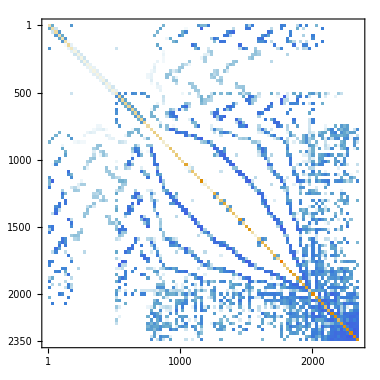
-Graphics- | -Graphics-

```mathematica
Grid[{{MatrixPlot[load(*, ColorFunction -> "Monochrome"*),ImageSize->55],MatrixPlot[stiffness(*, ColorFunction -> "Monochrome"*),ImageSize->380]}}]
```

#### 2.2.2 离散化边界条件

```mathematica
discreteBCs=DiscretizeBoundaryConditions[initBCs,methodData,sd]
{discreteBCs["LoadVector"],discreteBCs["StiffnessMatrix"]}
{discreteBCs["DirichletMatrix"],discreteBCs["DirichletValues"]}
```

DiscretizedBoundaryConditionData[<2350>]

{SparseArray[…],SparseArray[…]}

{SparseArray[…],SparseArray[…]}

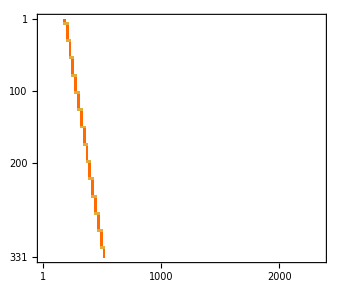
-Graphics- | -Graphics-

```mathematica
Grid[{{MatrixPlot[discreteBCs["DirichletMatrix"],ImageSize->340],MatrixPlot[discreteBCs["DirichletValues"],ImageSize->43]}}]
```

### 2.3 求解 (Solution Stage)

#### 2.3.1 配置边界条件 (Deploy Boundary Conditions)

DeployedBoundaryConditionData[<Insert>]

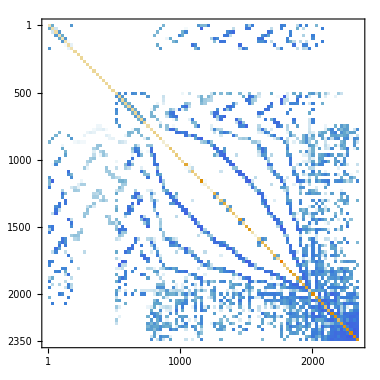
-Graphics- | -Graphics-

```mathematica
DeployBoundaryConditions[{load, stiffness}, discreteBCs]
Grid[{{MatrixPlot[load,ImageSize->55], MatrixPlot[stiffness,ImageSize->380]}}]
```

#### 2.3.2 解方程组 (Equation solving)

```mathematica
Short[solution = LinearSolve[stiffness, load]]
```

{{3.62147},{3.62147},{3.62146},«2344»,{2.91668},{0.643413},{-1.81329}}

### 2.4 后处理 (Post-Processing)

{InterpolatingFunction[…]}

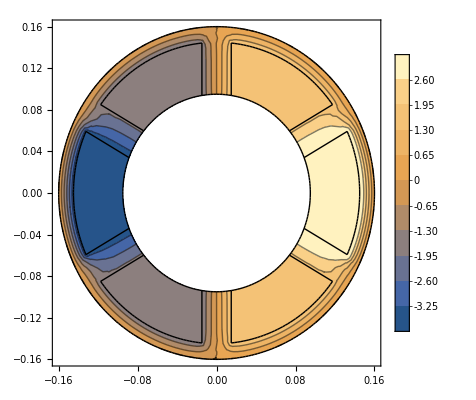

```mathematica
NDSolve`SetSolutionDataComponent[sd, "DependentVariables", Flatten[solution]];
{ifun}=ProcessPDESolutions[methodData,sd]
Show[ContourPlot[ifun[x,y],{x,y}∈mesh,Contours->10,PlotLegends->Automatic],bmesh["Wireframe"]]
```

## 3. 有限元与解析法的耦合与应用

### 3.1 课题组的工作

有限元分析是精确但费时的，课题组试图把有限元与速度更快但精度不够的解析法结合，以期在确保精度的前提下提高速度。

-Graphics-

### 3.2 解析法原理与实现

#### 3.2.1 解析法原理

控制方程：

永磁体区域：(∂^2 A)/(∂r^2)+1/r(∂A)/(∂r)+1/r^2(∂^2 A)/(∂φ^2)=1/r(∂B_Rr)/(∂φ)-1/r B_Rφ-(∂B_Rφ)/(∂r)
		气隙区域：(∂^2 A)/(∂r^2)+1/r(∂A)/(∂r)+1/r^2(∂^2 A)/(∂φ^2)=0

通解

A_i=a_i0 ln(r)+b_i0+∑_(k=1)^∞ [(a_ik r^k+b_ik r^-k+P_ck(r))cos(kφ)+(c_ik r^k+d_ik r^-k+P_sk(r))sin(kφ)]

边界条件

B_n1=B_n2
		H_t1=H_t2

#### 3.2.2 解析法矩阵生成

```mathematica
Subscript[r, 1]=r1=0.083;Subscript[r, 2]=r2=0.0945;Subscript[r, 3]=r3=0.095;Subscript[r, 4] =r4= 0.145;Subscript[r, 5]=r5=0.160;
rpn[i_,j_]=Table[If[k==l,If[k==0,(*Log[Subscript[r, i]/Subscript[rN, j]]*)0,(Subscript[r, i]/Subscript[rN, j])^k],0],{k,0,n},{l,0,n}];
rnn[i_,j_]= Table[If[k==l,If[k==0,0,(Subscript[r, i]/Subscript[rN, j])^-k],0],{k,0,n},{l,0,n}](* Table[If[k==l,(Subscript[r, i]/Subscript[rN, j])^-k,0],{k,0,n},{l,0,n}]*);
rnd[i_,j_]:= D[rpn[ni,j],Subscript[r, ni]]/.Subscript[r, ni]->Subscript[r, i];(*derivative*)
rnnd[i_,j_]:=D[rnn[ni,j],Subscript[r, ni]]/.Subscript[r, ni]->Subscript[r, i]; 
frn[n_]:=Piecewise[{{2(π η+Sin[π η])/(2π), Abs[p q n]==1}, {2(2p (q n Cos[(π η)/(2p)] Sin[(π η q n)/(2p)]-Cos[(π η q n)/(2p)] Sin[(π η)/(2p)]))/(π(q^2 n^2-1)), (q n)/(2p)-1/2∈Integers∧Abs[p q n]≠1}, {0, True}}]

fφn[n_]:=Piecewise[{{-2 n (π η-Sin[π η])/(2π), Abs[p q n]==1}, {-2 p/π(Sin[(π η( q n-1))/(2p)]/(q n-1)-Sin[(π η( q n+1))/(2p)]/(q n+1)), (q n)/(2p)-1/2∈Integers∧Abs[p q n]≠1}, {0, True}}]
bRr[n_,m_]:=Piecewise[{{bR*frn[n], m==0}, {0, m≠0}}]
bRφ[n_,m_]:=Piecewise[{{bR*fφn[n], m==0}, {0, m≠0}}]
p1[n_,m_,r_]:=Piecewise[{{(-n q bRr[n,m]-bRφ[n,m])(r Log[r])/2, n q==-1∨n q==1}, {(-n q bRr[n,m]- bRφ[n,m])r/(1-q^2 n^2), n q≠-1∧n q≠1}}]
p1d[n_,m_,r_]:=Piecewise[{{(-n q bRr[n,m]- bRφ[n,m])(Log[r]+1)/2, n q==-1∨n q==1}, {(-n q bRr[n,m]- bRφ[n,m]) 1/(1-q^2 n^2), n q≠-1∧n q≠1}}]
stiffnessOfAnalytical=Table[0,{i,1,3(2n+2)},{j,1,4(2 n+2)}];
(*Boundary Condition r1, an,bn*)
stiffnessOfAnalytical⟦1;;n+1,1;;n+1⟧=rnd[1,1];
stiffnessOfAnalytical⟦1;;n+1,n+2;;2n+2⟧=rnnd[1,1];
(*Boundary Condition r1, cn,dn*)
stiffnessOfAnalytical⟦n+2;;2n+2,2n+3;;3n+3⟧=rnd[1,1];
stiffnessOfAnalytical⟦n+2;;2n+2,3n+4;;4n+4⟧=rnnd[1,1];
(*Boundary Condition r2, Neumann, an,bn*)
stiffnessOfAnalytical⟦2 n+3;;3 n+3,1;;n+1⟧=1/μ1 rnd[2,1];
stiffnessOfAnalytical⟦2 n+3;;3n+3,n+2;;2n+2⟧=1/μ1 rnnd[2,1];
stiffnessOfAnalytical⟦2 n+3;;3 n+3,4 n+5;;5 n+5⟧=-rnd[2,2];
stiffnessOfAnalytical⟦2 n+3;;3 n+3,5 n+6;;6 n+6⟧=-rnnd[2,2];
(*Boundary Condition r2, Neumann, cn,dn*)
stiffnessOfAnalytical⟦3 n+4;;4 n+4,2 n+3;;3 n+3⟧=1/μ1 rnd[2,1];
stiffnessOfAnalytical⟦3 n+4;;4 n+4,3 n+4;;4n+4⟧=1/μ1 rnnd[2,1];
stiffnessOfAnalytical⟦3 n+4;;4 n+4,6 n+7;;7 n+7⟧=-rnd[2,2];
stiffnessOfAnalytical⟦3 n+4;;4 n+4,7 n+8;;8 n+8⟧=-rnnd[2,2];
(*Boundary Condition r2, Dirichlet, an,bn*)
stiffnessOfAnalytical⟦4n+5;;5n+5,1;;n+1⟧=rpn[2,1];
stiffnessOfAnalytical⟦4n+5;;5n+5,n+2;;2 n+2⟧=rnn[2,1];
stiffnessOfAnalytical⟦4n+5;;5n+5,4 n+5;;5 n+5⟧=-rpn[2,2];
stiffnessOfAnalytical⟦4n+5;;5n+5,5 n+6;;6 n+6⟧=-rnn[2,2];
(*Boundary Condition r2, Dirichlet, cn,dn*)
stiffnessOfAnalytical⟦5n+6;;6n+6,2 n+3;;3 n+3⟧=rpn[2,1];
stiffnessOfAnalytical⟦5n+6;;6n+6,3 n+4;;4 n+4⟧=rnn[2,1];
stiffnessOfAnalytical⟦5n+6;;6n+6,6 n+7;;7 n+7⟧=-rpn[2,2];
stiffnessOfAnalytical⟦5n+6;;6n+6,7 n+8;;8 n+8⟧=-rnn[2,2];
loadOfAnalytical=Table[0,{i,1,3(2 n+2)},{j,1,1}];
loadOfAnalytical⟦n+2;;2 n+2⟧=-Table[bRφ[i,0]+p1d[i,0,r1],{i,0,n},{j,1,1}];
loadOfAnalytical⟦3 n+4;;4 n+4⟧=-1/μ1*Table[bRφ[i,0]+p1d[i,0,r2],{i,0,n},{j,1,1}];
loadOfAnalytical⟦5 n+6;;6 n+6⟧=-Table[p1[i,0,r2],{i,0,n},{j,1,1}];
```

```mathematica
Grid[{{MatrixPlot[stiffnessOfAnalytical, ColorFunction -> "Monochrome",ImageSize->380], MatrixPlot[loadOfAnalytical, ColorFunction -> "Monochrome",ImageSize->43.5]}}]
```

-Graphics- | -Graphics-

### 3.3 耦合的实现

有限元程序包提供的内置函数能够输出有限元的矩阵，并且允许用户对矩阵进行修改。

#### 3.3.1生成初始矩阵

未知参数数量=4 ×(n+1)×2+有限元模型节点数

网格节点数量

```mathematica
numberOfElements=Length[stiffness];
```

```mathematica
boundaryEles=mesh["BoundaryElements"];
numberOfInnerBEs=Count[boundaryEles⟦1,2⟧,1];
numberOfElements=Length[stiffness];
numberOfInnerBPs=Count[boundaryEles⟦1,2⟧,1];
numberOfInnerBCEs=Count[boundaryEles⟦1,2⟧,1];
innerBEs=boundaryEles⟦1,1⟧⟦1;;numberOfInnerBEs,;;⟧;
beCoordatinates=mesh["Coordinates"]⟦1;;numberOfInnerBPs,;;⟧;
angleOfBPs=Table[If[ArcTan[beCoordatinates⟦n,1⟧,beCoordatinates⟦n,2⟧]<ArcTan[beCoordatinates⟦1,1⟧,beCoordatinates⟦1,2⟧],ArcTan[beCoordatinates⟦n,1⟧,beCoordatinates⟦n,2⟧]+2π,ArcTan[beCoordatinates⟦n,1⟧,beCoordatinates⟦n,2⟧]],{n,1,numberOfInnerBPs}];
distanceOfBEs=Table[√((beCoordatinates⟦innerBEs⟦j,1⟧,1⟧-beCoordatinates⟦innerBEs⟦j,2⟧,1⟧)^2+(beCoordatinates⟦innerBEs⟦j,1⟧,2⟧-beCoordatinates⟦innerBEs⟦j,2⟧,2⟧)^2),{j,1,numberOfInnerBEs}];
beCoordatinates=mesh["Coordinates"]⟦1;;numberOfInnerBCEs,;;⟧;
angleOfBCE=Table[If[ArcTan[beCoordatinates⟦n,1⟧,beCoordatinates⟦n,2⟧]<ArcTan[beCoordatinates⟦1,1⟧,beCoordatinates⟦1,2⟧],ArcTan[beCoordatinates⟦n,1⟧,beCoordatinates⟦n,2⟧]+2π,ArcTan[beCoordatinates⟦n,1⟧,beCoordatinates⟦n,2⟧]],{n,1,numberOfInnerBCEs}];
boundaryCons=Table[{If[1≤mesh["BoundaryConnectivity"]⟦n,1⟧≤numberOfInnerBCEs,mesh["BoundaryConnectivity"]⟦n,1⟧,mesh["BoundaryConnectivity"]⟦n,2⟧],If[1≤mesh["BoundaryConnectivity"]⟦n,3⟧≤numberOfInnerBCEs,mesh["BoundaryConnectivity"]⟦n,3⟧,mesh["BoundaryConnectivity"]⟦n,2⟧]},{n,1,numberOfInnerBCEs}];
distanceOfBCEs[i_,j_]:=√((beCoordatinates⟦i,1⟧-beCoordatinates⟦j,1⟧)^2+(beCoordatinates⟦i,2⟧-beCoordatinates⟦j,2⟧)^2)
```

```mathematica
numberOfElements
```

2350

生成矩阵

```mathematica
finalMatrix=Table[0,{i,1,8 n+8+numberOfElements},{j,1,8 n+8+numberOfElements}];
finalVector=Table[0,{i,1,4(2n+2)+numberOfElements},{j,1,1}];
```

放入已知的方程组

```mathematica
finalMatrix⟦1;;6n+6,1;;8n+8⟧=stiffnessOfAnalytical;
finalMatrix⟦8n+9;;8n+8+numberOfElements,8n+9;;8n+8+numberOfElements⟧=stiffness;
finalVector⟦1;;6n+6⟧=loadOfAnalytical;
finalVector⟦8n+9;;8n+8+numberOfElements⟧=load;
```

```mathematica
Grid[{{MatrixPlot[finalMatrix,ColorFunction->"Monochrome",ImageSize->380],MatrixPlot[finalVector,ColorFunction->"Monochrome",ImageSize->55]}}]
```

-Graphics- | -Graphics-

#### 3.3.2 边界条件处理

-Graphics-

磁感应强度的法向分量在分界面处连续 (B_n1=B_n2)

A_1=A_2

一次插值

f_n(φ)=(A^(n+1)-A^n)/(φ^(n+1)-φ^n)φ+(φ^(n+1)A^n-φ^n A^(n+1))/(φ^(n+1)-φ^n)

有限元侧的傅里叶级数

A_ck=1/T∑_(n=1)^N ∫_(n/N T)^((n+1)/N T) f_n(φ)cos(kφ)dφ
		A_sk=1/T∑_(n=1)^N ∫_(n/N T)^((n+1)/N T) f_n(φ)sin(kφ)dφ

两侧傅里叶级数相等

a_(2k)r^k+b_(2k)r^-k+P_ck(r)=1/T∑_(n=1)^N ∫_(n/N T)^((n+1)/N T) f_n(φ)cos(kφ)dφ
		c_(2k)r^k+d_(2k)r^-k+P_sk(r)=1/T∑_(n=1)^N ∫_(n/N T)^((n+1)/N T) f_n(φ)sin(kφ)dφ

放入矩阵中空白的位置

```mathematica
finalMatrix⟦6 n+7;;7 n+7,4 n+5;;5 n+5⟧=rpn[3,2];finalMatrix⟦6 n+7;;7 n+7,5 n+6;;6 n+6⟧=rnn[3,2];
finalMatrix⟦6n+7;;7n+7,8n+9;;8n+8+numberOfInnerBPs⟧=-1/π*Table[If[i==0,If[j==1,(angleOfBPs⟦2⟧-angleOfBPs⟦1⟧)/2+((angleOfBPs⟦1⟧+2π)-angleOfBPs⟦numberOfInnerBPs⟧)/2,If[j==numberOfInnerBPs,((angleOfBPs⟦1⟧+2π)-angleOfBPs⟦j-1⟧)/2,(angleOfBPs⟦j+1⟧-angleOfBPs⟦j-1⟧)/2]],If[j==1,(-Cos[i angleOfBPs⟦j⟧]+Cos[i angleOfBPs⟦j+1⟧])/(q^2 i^2(angleOfBPs⟦j⟧-angleOfBPs⟦j+1⟧))+(Cos[i angleOfBPs⟦numberOfInnerBPs⟧]-Cos[i (angleOfBPs⟦1⟧+2π)])/(q^2 i^2(angleOfBPs⟦numberOfInnerBPs⟧-(angleOfBPs⟦1⟧+2π))),If[j==numberOfInnerBPs,(-Cos[i angleOfBPs⟦j⟧]+Cos[i (angleOfBPs⟦1⟧+2π)])/(q^2 i^2(angleOfBPs⟦j⟧-(angleOfBPs⟦1⟧+2π)))+(Cos[i angleOfBPs⟦j-1⟧]-Cos[i angleOfBPs⟦j⟧])/(q^2 i^2(angleOfBPs⟦j-1⟧-angleOfBPs⟦j⟧)),(-Cos[i angleOfBPs⟦j⟧]+Cos[i angleOfBPs⟦j+1⟧])/(q^2 i^2(angleOfBPs⟦j⟧-angleOfBPs⟦j+1⟧))+(Cos[i angleOfBPs⟦j-1⟧]-Cos[i angleOfBPs⟦j⟧])/(q^2 i^2(angleOfBPs⟦j-1⟧-angleOfBPs⟦j⟧))]]],{i,0,n},{j,1,numberOfInnerBPs}];
finalMatrix⟦7 n+8;;8 n+8,6 n+7;;7 n+7⟧=rpn[3,2];finalMatrix⟦7 n+8;;8 n+8,7 n+8;;8 n+8⟧=rnn[3,2];
finalMatrix⟦7n+8;;8n+8,8n+9;;8n+8+numberOfInnerBPs⟧=-1/π*Table[If[i==0,0,If[j==1,-(Sin[i angleOfBPs⟦j⟧]-Sin[i angleOfBPs⟦j+1⟧])/(q^2 i^2(angleOfBPs⟦j⟧-angleOfBPs⟦j+1⟧))+(Sin[i angleOfBPs⟦numberOfInnerBPs⟧]-Sin[i (angleOfBPs⟦1⟧+2π)])/(q^2 i^2(angleOfBPs⟦numberOfInnerBPs⟧-(angleOfBPs⟦1⟧+2π))),If[j==numberOfInnerBPs,-(Sin[i angleOfBPs⟦j⟧]-Sin[i (angleOfBPs⟦1⟧+2π)])/(q^2 i^2(angleOfBPs⟦j⟧-(angleOfBPs⟦1⟧+2π)))+(Sin[i angleOfBPs⟦j-1⟧]-Sin[i angleOfBPs⟦j⟧])/(q^2 i^2(angleOfBPs⟦j-1⟧-angleOfBPs⟦j⟧)),-(Sin[i angleOfBPs⟦j⟧]-Sin[i angleOfBPs⟦j+1⟧])/(q^2 i^2(angleOfBPs⟦j⟧-angleOfBPs⟦j+1⟧))+(Sin[i angleOfBPs⟦j-1⟧]-Sin[i angleOfBPs⟦j⟧])/(q^2 i^2(angleOfBPs⟦j-1⟧-angleOfBPs⟦j⟧))]]],{i,0,n},{j,1,numberOfInnerBPs}];
```

```mathematica
Grid[{{MatrixPlot[finalMatrix,ColorFunction->"Monochrome",ImageSize->380],MatrixPlot[finalVector,ColorFunction->"Monochrome",ImageSize->55]}}]
```

-Graphics- | -Graphics-

磁场强度的切向分量在分界面处连续 (H_t1=H_t2)

1/μ_1(∂A_1)/(∂n)=1/μ_2(∂A_2)/(∂n)

有限元处理                                                                             -Graphics-

1/μ_2(∂A_2)/(∂n)=q
		[K]_e{A}_e={q}_e+{q'}_e                  {q'}_e={0
(q_a l_0)/2
(q_a l_0)/2}

[K]{A}={q}+{q'}
		{q'}=[Q]{C}
		-[Q]{C}+[K]{A}={q}

放入矩阵中空白的位置

```mathematica
finalMatrix⟦8 n+9;;8 n+8+numberOfInnerBCEs,4 n+5;;5 n+5⟧=1/μAir Table[If[i==0,0,If[j==1,(q i)/rN2(r3/rN2)^(q i-1)Cos[i angleOfBPs⟦j⟧]r3 ((angleOfBPs⟦j+1⟧+2π)-angleOfBPs⟦numberOfInnerBPs⟧)/2 ,If[j== numberOfInnerBPs,(q i)/rN2(r3/rN2)^(q i-1)Cos[i angleOfBPs⟦j⟧]r3 ((angleOfBPs⟦1⟧+2π)-angleOfBPs⟦j-1⟧)/2,(q i)/rN2(r3/rN2)^(q i-1)Cos[i angleOfBPs⟦j⟧]r3 (angleOfBPs⟦j+1⟧-angleOfBPs⟦j-1⟧)/2]]],{j,1,numberOfInnerBPs},{i,0,n}];
finalMatrix⟦8 n+9;;8 n+8+numberOfInnerBCEs,5 n+6;;6 n+6⟧=1/μAir Table[If[i==0,0,If[j==1,(-q i)/rN2(r3/rN2)^(-q i-1)Cos[i angleOfBPs⟦j⟧]r3 ((angleOfBPs⟦j+1⟧+2π)-angleOfBPs⟦numberOfInnerBPs⟧)/2,If[j== numberOfInnerBPs,(-q i)/rN2(r3/rN2)^(-q i-1)Cos[i angleOfBPs⟦j⟧]r3 ((angleOfBPs⟦1⟧+2π)-angleOfBPs⟦j-1⟧)/2,(-q i)/rN2(r3/rN2)^(-q i-1)Cos[i angleOfBPs⟦j⟧]r3 (angleOfBPs⟦j+1⟧-angleOfBPs⟦j-1⟧)/2]]],{j,1,numberOfInnerBPs},{i,0,n}];
finalMatrix⟦8 n+9;;8 n+8+numberOfInnerBCEs,6 n+7;;7 n+7⟧=1/μAir Table[If[i==0,0,If[j==1,(q i)/rN2(r3/rN2)^(q i-1)Sin[i angleOfBPs⟦j⟧]r3 ((angleOfBPs⟦j+1⟧+2π)-angleOfBPs⟦numberOfInnerBPs⟧)/2,If[j== numberOfInnerBPs,(q i)/rN2(r3/rN2)^(q i-1)Sin[i angleOfBPs⟦j⟧]r3 ((angleOfBPs⟦1⟧+2π)-angleOfBPs⟦j-1⟧)/2,(q i)/rN2(r3/rN2)^(q i-1)Sin[i angleOfBPs⟦j⟧]r3 (angleOfBPs⟦j+1⟧-angleOfBPs⟦j-1⟧)/2]]],{j,1,numberOfInnerBPs},{i,0,n}];
finalMatrix⟦8 n+9;;8 n+8+numberOfInnerBCEs,7 n+8;;8 n+8⟧=1/μAir Table[If[i==0,0,If[j==1,-(q i)/rN2(r3/rN2)^(-q i-1)Sin[i angleOfBPs⟦j⟧]r3 ((angleOfBPs⟦j+1⟧+2π)-angleOfBPs⟦numberOfInnerBPs⟧)/2,If[j== numberOfInnerBPs,-(q i)/rN2(r3/rN2)^(-q i-1)Sin[i angleOfBPs⟦j⟧]r3 ((angleOfBPs⟦1⟧+2π)-angleOfBPs⟦j-1⟧)/2,-(q i)/rN2(r3/rN2)^(-q i-1)Sin[i angleOfBPs⟦j⟧]r3 (angleOfBPs⟦j+1⟧-angleOfBPs⟦j-1⟧)/2]]],{j,1,numberOfInnerBPs},{i,0,n}];
```

```mathematica
Grid[{{MatrixPlot[finalMatrix,ColorFunction->"Monochrome",ImageSize->380],MatrixPlot[finalVector,ColorFunction->"Monochrome",ImageSize->55]}}]
```

-Graphics- | -Graphics-

#### 3.3.3 求解

```mathematica
Short[solution=LinearSolve[finalMatrix,finalVector]]
```

{{0.},{0.0196915},{-0.000241937},{-0.0000134488},«3095»,{0.0472005},{-0.00575324},{0.0156293}}

#### 3.3.4后处理

有限元部分输出

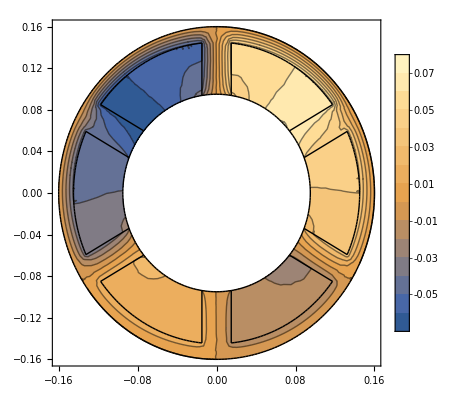

```mathematica
feaSolution=solution⟦8n+9;;8n+8+numberOfElements⟧;
NDSolve`SetSolutionDataComponent[sd,"DependentVariables",Flatten[feaSolution]];
{ifun}=ProcessPDESolutions[methodData,sd];
contour=Table[n,{n,-0.07,0.07,0.01}];
Show[ContourPlot[ifun[x,y],{x,y}∈mesh,Contours->contour,PlotLegends->Automatic],bmesh["Wireframe"]]
```

全区域输出

```mathematica
-Graphics--Graphics-
```

气隙磁场对比

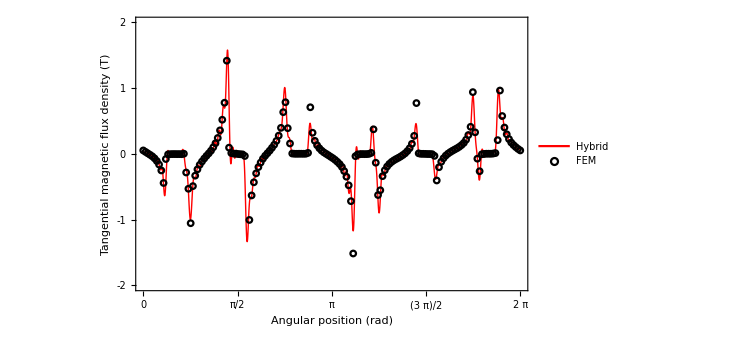
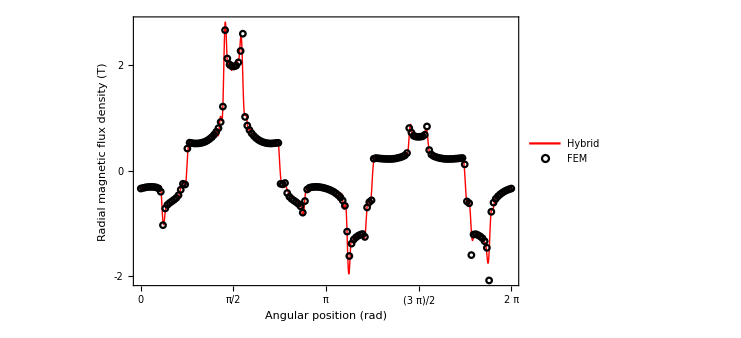

## 4.总结

有限元方法以变分原理为基础，将待求解的微分方程数学模型转化为相应的变分问题，然后利用剖分，离散化为多元函数的极值问题，最终转化为多元代数方程组，求解就可得到微分方程的数值解。

Wolfram有限元程序包提供的内置函数允许用户对计算过程进行控制。

用户可以利用有限元程序包生成的矩阵，将有限元与其他计算方法进行耦合，这样的耦合使得计算所需的时间大大减少，同时也保证了精度。

待改进的地方：Wolfram程序包提供的periodical boundary condition不是通常有限元意义上的周期性边界条件，如果能够实现周期性边界条件，计算能够更简练。